### Inclusion of the Coulomb interaction

The equation we need to solve is Δ_k=Σ_k' Δ_k'/(√(Δ_k'^2+((k'-p_0)^2/(2m)-Λ)^2))(g-v_(k-k')Cos(θ_k-θ_k')). The integral can be turned into a 1D one by performing angular average: Δ_k=p_0/(2Pi)∫dk' Δ_k'/(√(Δ_k'^2+((k'-p_0)^2/(2m)-Λ)^2))(g-v_(k,k')). 
Here v_(k,k')=1/(2π)∫dθ (2π e^2 Cosθ)/(√(k^2+(k')^2-2k k' Cosθ))

## Pair density with Coulomb interaction

```mathematica
PairDensity[Λ_,g_,Ec_,d_,Nit_]:=Module[{i,pmax=3.,dp=.05,meshp,Δ,δ,ϵ=10^-6.,p,q,CKernel,CKernelCos,ξ,pvec,unitvec,Φ,cutoff},
meshp=Range[0,pmax,dp];
(*Calculate the Coulomb kernel*)
CKernel=ParallelTable[Quiet[NIntegrate[Ec/(2Pi)(1-Exp[-d √(p^2+q^2-2 p q Cos[θ])])/(√(ϵ+p^2+q^2-2 p q Cos[θ])),{θ,0,2Pi}]],{p,0,pmax,dp},{q,0,pmax,dp}]//Chop;
CKernelCos=ParallelTable[Quiet[NIntegrate[Ec/(2Pi)(Cos[θ](1-Exp[-d √(p^2+q^2-2 p q Cos[θ])]))/(√(ϵ+p^2+q^2-2 p q Cos[θ])),{θ,0,2Pi}]],{p,0,pmax,dp},{q,0,pmax,dp}]//Chop;
(*Create the vector of ξ and p*)
ξ=(1/2(#-1)^2-Λ)&/@meshp;
pvec=meshp;
unitvec=1.&/@meshp;(*To calculate sum over momenta*)
(*cutoff=Exp[(-(pvec-unitvec)^2)/2];
pvec=pvec*cutoff;*)
(*Iterate to obtain Δ and Φ*)
Δ=.0001&/@meshp;
Φ=0.0&/@meshp;

For[i=0,i<Nit,i++,
Δ=dp/(2*2Pi)*unitvec(unitvec.(g (pvec Δ)/(√((ξ+Φ)^2+Δ^2))))-dp/(2*2Pi)*CKernelCos.((pvec Δ)/(√((ξ+Φ)^2+Δ^2)));
Φ=(dp/(2*2Pi)*unitvec(unitvec.((Ec d pvec)/(2Pi) (1-(ξ+Φ)/(√((ξ+Φ)^2+Δ^2)))))-dp/(2*2Pi)*CKernel.(pvec*(1-(ξ+Φ)/(√((ξ+Φ)^2+Δ^2)))));];
{Δ,Φ,unitvec.(dp/(2*2Pi) (pvec Δ)/(√((ξ+Φ)^2+Δ^2)))}

]
```

```mathematica
(*List0={#,PairDensity[#,0.33,0.0,10.,100][[3]]}&/@Range[-.025,.0,0.00033];
List1={#,PairDensity[#,0.33,0.13,10.,100][[3]]}&/@Range[-.025,.0,0.00033];
List2={#,PairDensity[#,0.33,0.23,10.,100][[3]]}&/@Range[-.025,.0,0.00033];*)
List3={#,PairDensity[#,0.33,0.4,10.,101][[3]]}&/@Range[-.0022,-0.0018,0.00001];
(*List4={#,PairDensity[#,0.33,0.5,10.,101][[3]]}&/@Range[-.005,.0,0.001];
List5={#,PairDensity[#,0.33,0.6,10.,101][[3]]}&/@Range[-.005,.0,0.001];*)
```

```mathematica
(*List00={#,PairDensity[#,0.33,0.0,10.,101][[3]]}&/@Range[-.1,.1,0.0033];
List11={#,PairDensity[#,0.33,0.13,10.,101][[3]]}&/@Range[-.1,.1,0.0033];
List22={#,PairDensity[#,0.33,0.23,10.,101][[3]]}&/@Range[-.1,.1,0.0033];
List33={#,PairDensity[#,0.33,0.33,10.,101][[3]]}&/@Range[-.1,.1,0.0033];
List44={#,PairDensity[#,0.33,0.43,10.,101][[3]]}&/@Range[-.1,.1,0.0033];*)
```

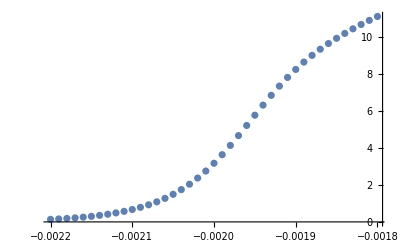

```mathematica
ListPlot[{(*List0,List1,List2,List3,List4,List5*)List3},Joined->False,PlotRange->All]
```

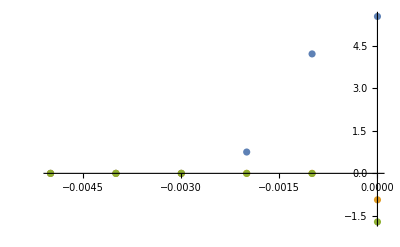

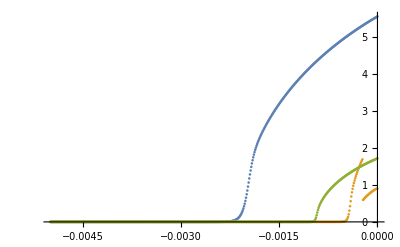

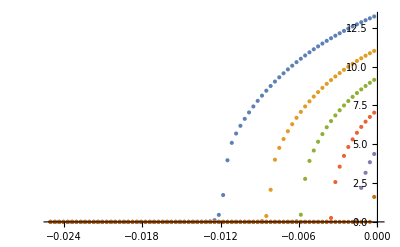

### Pairing without Coulomb - test case

```mathematica
PairDensityNoC[Λ_,g_,Nit_]:=Module[{i,pmax=5.,dp=.01,meshp,Δ,δ,ϵ=10^-6.,p,q,CKernel,CKernelCos,ξ,pvec,unitvec,Φ,cutoff},
meshp=Range[0,pmax,dp];

(*Create the vector of ξ and p*)
ξ=(1/2(#-1)^2-Λ)&/@meshp;
pvec=meshp;
unitvec=1.&/@meshp;(*To calculate sum over momenta*)
(*cutoff=Exp[(-(pvec-unitvec)^2)/2];
pvec=pvec*cutoff;*)
(*Iterate to obtain Δ and Φ*)
Δ=.0001&/@meshp;

For[i=0,i<Nit,i++,
Δ=dp/(2*2Pi)*unitvec(unitvec.(g (pvec Δ)/(√((ξ)^2+Δ^2))));];
unitvec.( dp/(2*2Pi)(pvec Δ)/(√((ξ)^2+Δ^2)))

]
```

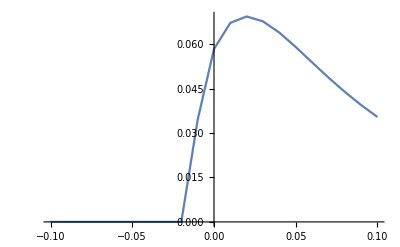

```mathematica
ListΔ={#,PairDensityNoC[#,0.33,301]}&/@Range[-.1,0.1,0.01];
ListPlot[ListΔ,Joined->True,PlotRange->All]
```

### Pairing without Coulomb - Gaussian quadrature

```mathematica
PairDensityNoC[Λ_,g_,Nit_]:=Module[{i,pmax=3.,np=80,dp=.05,meshp,Δ,δ,ϵ=10^-6.,p,q,CKernel,CKernelCos,ξ,pvec,unitvec,Φ,cutoff,roots,weights,resΔ},
(*Collocation points: roots of np's Legendre polynomial*)
roots=N[Root[LegendreP[np,x],#]]&/@Range[1,np];
(*Weights for Gauss-Legendre quadrature*)
weights=(2(1-roots^2))/((np+1)^2 LegendreP[np+1,roots]^2);
meshp=(pmax-0)/2 roots+(pmax+0)/2;

(*Create the vectors of ξ and p*)
ξ=(1/2(#-1)^2-Λ)&/@meshp;
pvec=meshp;
unitvec=1.&/@meshp;(*To calculate sum over momenta*)

(*Iterate to obtain Δ and Φ*)
Δ=.0001&/@meshp;

For[i=0,i<Nit,i++,
Δ=(pmax-0)/2 1/(2*2Pi)*unitvec(unitvec.(g weights(pvec Δ)/(√((ξ)^2+Δ^2))));];
resΔ={meshp[[#]],Δ[[#]]}&/@Range[1,Length[meshp]];
{resΔ,unitvec.( 1/(2* 2Pi)weights(pvec Δ)/(√((ξ)^2+Δ^2)))}

]
```

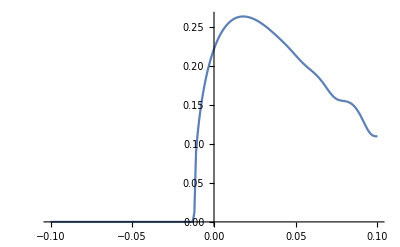

```mathematica
ListΔ={#,PairDensityNoC[#,0.33,101][[2]]}&/@Range[-.1,0.1,0.001];
ListPlot[ListΔ,Joined->True,PlotRange->All]
```

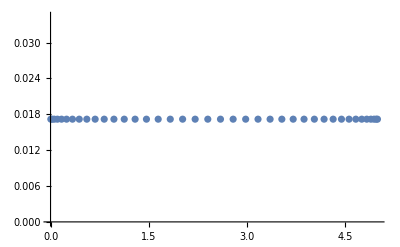

```mathematica
PairDensityNoC[0.1,0.33,100][[1]]//ListPlot
```

### Pairing without Coulomb - NIntegrate

```mathematica
PairDensityNoC[Λ_,g_,Nit_]:=Module[{i,pmax=5.,dp=.05,meshp,Δ,δ,ϵ=10^-6.,p,q,CKernel,CKernelCos,ξ,pvec,unitvec,Φ,cutoff,x},
meshp=Range[0,pmax,dp];

(*Create the vector of ξ and p*)
ξ[x_]:=(1/2(x-1)^2-Λ);
pvec=meshp;
unitvec=1.&/@meshp;(*To calculate sum over momenta*)
(*cutoff=Exp[(-(pvec-unitvec)^2)/2];
pvec=pvec*cutoff;*)
(*Iterate to obtain Δ and Φ*)
Δ=.0001;

For[i=0,i<Nit,i++,
Δ=1/(2*2Pi)*g Δ NIntegrate[1/(√((ξ[x])^2+Δ^2)),{x,0,pmax}]//Quiet;];
NIntegrate[1/(2*2Pi)Δ/(√((ξ[x])^2+Δ^2)),{x,0,pmax}]//Quiet

]
```

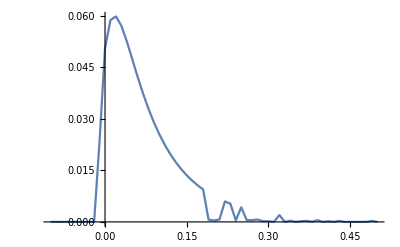

```mathematica
ListΔ={#,PairDensityNoC[#,0.33,101]}&/@Range[-.1,0.5,0.01];
ListPlot[ListΔ,Joined->True,PlotRange->All]
```

## Calculation at a given d: pre-saved kernels

```mathematica
dp=.01;
pmax=2.;
ϵ=10^-10.;
d=10.;
CKernelPre=ParallelTable[Quiet[NIntegrate[1/(2Pi)(1-Exp[-d √(p^2+q^2-2 p q Cos[θ])])/(√(ϵ+p^2+q^2-2 p q Cos[θ])),{θ,0,2Pi}]],{p,0,pmax,dp},{q,0,pmax,dp}]//Chop;
CKernelCosPre=ParallelTable[Quiet[NIntegrate[1/(2Pi)(Cos[θ](1-Exp[-d √(p^2+q^2-2 p q Cos[θ])]))/(√(ϵ+p^2+q^2-2 p q Cos[θ])),{θ,0,2Pi}]],{p,0,pmax,dp},{q,0,pmax,dp}]//Chop;
```

```mathematica
ListContourPlot[CKernelCosPre,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[CKernelPre,PlotLegends->Automatic]
```

-Graphics-

```mathematica
PairDensity[Λ_,g_,Ec_,Nit_]:=Module[{i,meshp,Δ,Δ0,δ,p,q,ξ,pvec,unitvec,Φ,Φ0,CKernelCos,CKernel,cutoff},
meshp=Range[0,pmax,dp];
(*REscale the Coulomb kernel*)
CKernelCos=Ec*CKernelCosPre;
CKernel=Ec*CKernelPre;
(*Create the vector of ξ and p*)
ξ=((#-1)^2+Λ)&/@meshp;
pvec=meshp;
unitvec=1.&/@meshp;(*To calculate sum over momenta*)
(*cutoff=Exp[(-(pvec-unitvec)^2)/2];
pvec=pvec*cutoff;*)
(*Iterate to obtain Δ and Φ*)
Δ=g^2/16&/@meshp;
Φ=0.0&/@meshp;

For[i=0,i<Nit,i++,
Φ0=(dp/(2*2Pi)*unitvec(unitvec.(Ec d pvec (1-(ξ+Φ)/(√((ξ+Φ)^2+Δ^2)))))-dp/(2*2Pi)*CKernel.(pvec*(1-(ξ+Φ)/(√((ξ+Φ)^2+Δ^2)))));
Δ0=dp/(2*2Pi)*unitvec(unitvec.(g (pvec Δ)/(√((ξ+Φ)^2+Δ^2))))-dp/(2*2Pi)*CKernelCos.((pvec Δ)/(√((ξ+Φ)^2+Δ^2)));
Δ=0.25Δ0+.75Δ;Φ =0.25Φ0+.75Φ;
];
{Δ,Φ,unitvec(dp/(2*2Pi)).( (pvec Δ)/(√((ξ+Φ)^2+Δ^2))),unitvec.((dp pvec)/(2*2Pi)(1- (ξ+Φ)/(√((ξ+Φ)^2+Δ^2)))),Min[Δ],Min[Φ]}
]
```

```mathematica
(*Δ=Δ0;Φ = Φ0;*)
```

```mathematica
minp = {#,PairDensity[0,0.33,#,2001][[6]]}&/@Range[0.48,0.5,0.0002];
```

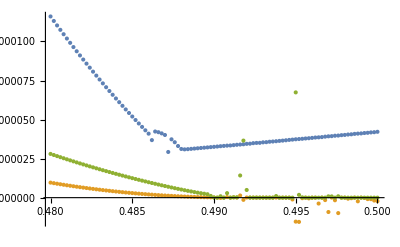

```mathematica
ListPlot[{minp,mind,n}]
```

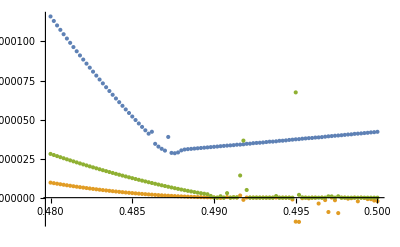

```mathematica
ListPlot[{minp,mind,n}]
```

```mathematica
AbsoluteTiming[ListsEc1st=Table[({#,(PairDensity[i,0.33,#,100][[3]]+PairDensity[i,0.33,#,101][[3]])/2}&/@Range[0.4,0.6,0.001]),{i,-0.001,0.001,0.0001}];]
```

{{0.3,0.0268446},{0.301,0.0267631},{0.302,0.0266816},{0.303,0.0265999},{0.304,0.026518},{0.305,0.026436},{0.306,0.0263538},{0.307,0.0262714},{0.308,0.0261889},{0.309,0.0261062},{0.31,0.0260234},{0.311,0.0259403},{0.312,0.0258572},{0.313,0.0257738},{0.314,0.0256903},{0.315,0.0256066},{0.316,0.0255228},{0.317,0.0254387},{0.318,0.0253545},{0.319,0.0252701},{0.32,0.0251856},{0.321,0.0251008},{0.322,0.0250159},{0.323,0.0249308},{0.324,0.0248455},{0.325,0.0247601},{0.326,0.0246744},{0.327,0.0245886},{0.328,0.0245026},{0.329,0.0244163},{0.33,0.0243299},{0.331,0.0242433},{0.332,0.0241565},{0.333,0.0240695},{0.334,0.0239823},{0.335,0.023895},{0.336,0.0238074},{0.337,0.0237196},{0.338,0.0236316},{0.339,0.0235434},{0.34,0.023455},{0.341,0.0233664},{0.342,0.0232775},{0.343,0.0231885},{0.344,0.0230992},{0.345,0.0230098},{0.346,0.0229201},{0.347,0.0228302},{0.348,0.0227401},{0.349,0.0226497},{0.35,0.0225591},{0.351,0.0224683},{0.352,0.0223773},{0.353,0.022286},{0.354,0.0221945},{0.355,0.0221028},{0.356,0.0220108},{0.357,0.0219186},{0.358,0.0218262},{0.359,0.0217335},{0.36,0.0216405},{0.361,0.0215474},{0.362,0.0214539},{0.363,0.0213602},{0.364,0.0212663},{0.365,0.0211721},{0.366,0.0210776},{0.367,0.0209829},{0.368,0.0208879},{0.369,0.0207927},{0.37,0.0206972},{0.371,0.0206014},{0.372,0.0205053},{0.373,0.020409},{0.374,0.0203124},{0.375,0.0202154},{0.376,0.0201183},{0.377,0.0200208},{0.378,0.019923},{0.379,0.019825},{0.38,0.0197266},{0.381,0.019628},{0.382,0.019529},{0.383,0.0194298},{0.384,0.0193302},{0.385,0.0192303},{0.386,0.0191301},{0.387,0.0190296},{0.388,0.0189288},{0.389,0.0188276},{0.39,0.0187262},{0.391,0.0186244},{0.392,0.0185222},{0.393,0.0184197},{0.394,0.0183169},{0.395,0.0182138},{0.396,0.0181102},{0.397,0.0180064},{0.398,0.0179022},{0.399,0.0177976},{0.4,0.0176926},{0.401,0.0175873},{0.402,0.0174816},{0.403,0.0173756},{0.404,0.0172692},{0.405,0.0171623},{0.406,0.0170551},{0.407,0.0169475},{0.408,0.0168395},{0.409,0.0167311},{0.41,0.0166223},{0.411,0.0165131},{0.412,0.0164035},{0.413,0.0162934},{0.414,0.0161829},{0.415,0.016072},{0.416,0.0159607},{0.417,0.0158489},{0.418,0.0157367},{0.419,0.015624},{0.42,0.0155108},{0.421,0.0153972},{0.422,0.0152831},{0.423,0.0151686},{0.424,0.0150535},{0.425,0.014938},{0.426,0.014822},{0.427,0.0147055},{0.428,0.0145885},{0.429,0.0144709},{0.43,0.0143529},{0.431,0.0142343},{0.432,0.0141152},{0.433,0.0139956},{0.434,0.0138754},{0.435,0.0137546},{0.436,0.0136333},{0.437,0.0135114},{0.438,0.0133889},{0.439,0.0132659},{0.44,0.0131422},{0.441,0.013018},{0.442,0.0128931},{0.443,0.0127676},{0.444,0.0126415},{0.445,0.0125148},{0.446,0.0123874},{0.447,0.0122593},{0.448,0.0121306},{0.449,0.0120012},{0.45,0.0118711},{0.451,0.0117403},{0.452,0.0116088},{0.453,0.0114766},{0.454,0.0113437},{0.455,0.01121},{0.456,0.0110755},{0.457,0.0109403},{0.458,0.0108043},{0.459,0.0106676},{0.46,0.01053},{0.461,0.0103916},{0.462,0.0102524},{0.463,0.0101123},{0.464,0.00997135},{0.465,0.00982955},{0.466,0.00968686},{0.467,0.00954326},{0.468,0.00939875},{0.469,0.00925331},{0.47,0.00910692},{0.471,0.00895956},{0.472,0.00881121},{0.473,0.00866187},{0.474,0.00851151},{0.475,0.00836011},{0.476,0.00820766},{0.477,0.00805414},{0.478,0.00789952},{0.479,0.00774379},{0.48,0.00758693},{0.481,0.00742892},{0.482,0.00726973},{0.483,0.00710935},{0.484,0.000178474},{0.485,0.0000637329},{0.486,0.0000351712},{0.487,0.0000233969},{0.488,0.0000154394},{0.489,9.50154×10^-6},{0.49,5.39117×10^-6},{0.491,2.8137×10^-6},{0.492,1.34186×10^-6},{0.493,5.7349×10^-7},{0.494,2.08488×10^-7},{0.495,5.38428×10^-8},{0.496,-1.34981×10^-9},{0.497,-1.48002×10^-8},{0.498,-1.36436×10^-8},{0.499,-9.15556×10^-9},{0.5,-5.19953×10^-9},{0.501,-2.59182×10^-9},{0.502,-1.12772×10^-9},{0.503,-4.05222×10^-10},{0.504,-9.46503×10^-11},{0.505,1.46211×10^-11},{0.506,3.83912×10^-11},{0.507,3.27195×10^-11},{0.508,2.11374×10^-11},{0.509,1.15712×10^-11},{0.51,5.47338×10^-12},{0.511,2.16371×10^-12},{0.512,6.10356×10^-13},{0.513,3.07848×10^-15},{0.514,-1.63271×10^-13},{0.515,-1.58912×10^-13},{0.516,-1.09055×10^-13},{0.517,-6.18104×10^-14},{0.518,-2.9633×10^-14},{0.519,-1.14529×10^-14},{0.52,-2.73978×10^-15},{0.521,5.98263×10^-16},{0.522,1.39797×10^-15},{0.523,1.19609×10^-15},{0.524,7.81059×10^-16},{0.525,4.11997×10^-16},{0.526,1.661×10^-16},{0.527,4.11997×10^-17},{0.528,-4.77049×10^-18},{0.529,-1.86483×10^-17},{0.53,-1.64799×10^-17},{0.531,-1.64799×10^-17},{0.532,-4.33681×10^-18},{0.533,-3.03577×10^-18},{0.534,8.67362×10^-19},{0.535,-1.73472×10^-18},{0.536,-8.67362×10^-19},{0.537,-1.73472×10^-18},{0.538,3.03577×10^-18},{0.539,-1.30104×10^-18},{0.54,0.},{0.541,-4.33681×10^-18},{0.542,2.60209×10^-18},{0.543,-2.60209×10^-18},{0.544,-1.73472×10^-18},{0.545,2.1684×10^-18},{0.546,4.33681×10^-19},{0.547,-8.67362×10^-19},{0.548,3.46945×10^-18},{0.549,1.73472×10^-18},{0.55,-8.67362×10^-19},{0.551,-1.30104×10^-18},{0.552,-2.60209×10^-18},{0.553,-8.67362×10^-19},{0.554,-1.73472×10^-18},{0.555,4.33681×10^-19},{0.556,-1.30104×10^-18},{0.557,-1.30104×10^-18},{0.558,3.46945×10^-18},{0.559,-2.60209×10^-18},{0.56,-1.30104×10^-18},{0.561,-8.67362×10^-19},{0.562,1.73472×10^-18},{0.563,8.67362×10^-18},{0.564,-4.33681×10^-19},{0.565,-8.67362×10^-19},{0.566,0.},{0.567,-8.67362×10^-19},{0.568,0.},{0.569,-1.73472×10^-18},{0.57,-1.73472×10^-18},{0.571,2.60209×10^-18},{0.572,7.80626×10^-18},{0.573,3.03577×10^-18},{0.574,0.},{0.575,-3.03577×10^-18},{0.576,6.50521×10^-18},{0.577,8.67362×10^-19},{0.578,1.73472×10^-18},{0.579,3.03577×10^-18},{0.58,0.},{0.581,3.90313×10^-18},{0.582,0.},{0.583,0.},{0.584,3.03577×10^-18},{0.585,3.90313×10^-18},{0.586,1.30104×10^-18},{0.587,4.33681×10^-19},{0.588,2.1684×10^-18},{0.589,1.73472×10^-18},{0.59,1.73472×10^-18},{0.591,8.67362×10^-19},{0.592,-8.67362×10^-19},{0.593,6.07153×10^-18},{0.594,2.1684×10^-18},{0.595,1.73472×10^-18},{0.596,3.03577×10^-18},{0.597,-8.67362×10^-19},{0.598,1.73472×10^-18},{0.599,4.33681×10^-19},{0.6,8.67362×10^-19}}

{494.77,Null}

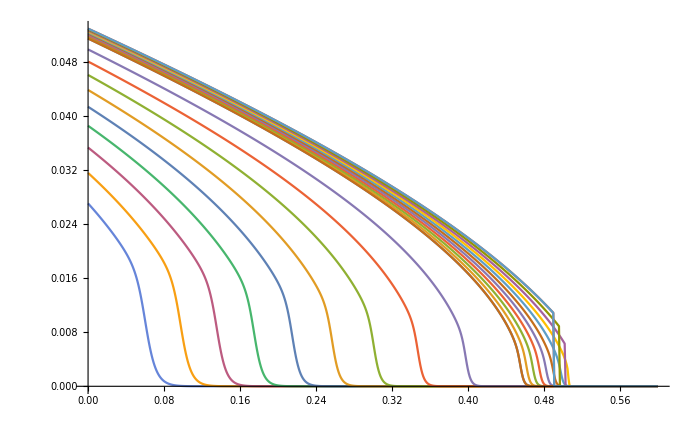

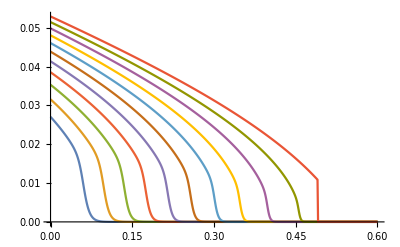

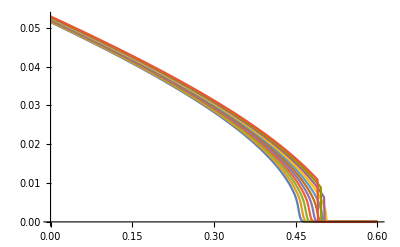

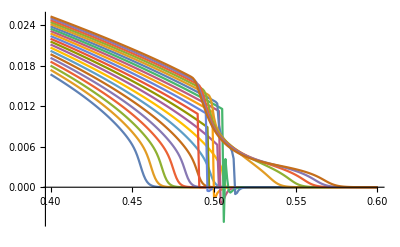

-Graphics-

```mathematica
ListPlot[Join[ListsEcFina,ListsEc],Joined->True,PlotRange->All]
ListPlot[ListsEc,Joined->True,PlotRange->All]
ListPlot[ListsEcFina,Joined->True,PlotRange->All]
ListPlot[ListsEc1st,Joined->True,PlotRange->All]
```

```mathematica
ListPlot[ListsEc1st,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
AbsoluteTiming[ListsΛ=Table[({#,(PairDensity[#,0.33,i,100][[3]]+PairDensity[#,0.33,i,101][[3]])/2}&/@Range[-0.001,0.001,0.00002]),{i,0.4,0.6,0.01}];]
```

{48976.6,Null}

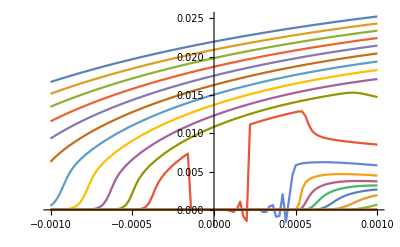

```mathematica
ListPlot[ListsΛ,Joined->True,PlotRange->All]
```